```mathematica
Clear[f, F, g, hh, bk, ck, hh, hk, k, u, b];

                                                                                                   (*Emile Timothy Anand*)
                                                                                                           (*Assignment 3*)
                                                                                                                  (*Topic 4*)

(* Part a *)

(* Sample Functions to be used: *)

(*f[x_]:=x^2*)

(*f[x_]:=E^x*)

(*f[x_]:= Sin[2 x]*)

f[x_] := Piecewise[{{1, x≤0.5}, {-1, x>0.5}}]
    
a[k_,L_] := 2/L*∫_0^L f[x]Cos[(2*k*Pi*x)/L] ⅆx         (* Defines the function Subscript[a, k]*)
A = Range[11];
For [i=0, i ≤ 10, i++, A[[i]] = a[i, 1]]         (* Precomputes Subscript[a, k] for k=1 to 10*)
b[k_,L_] := 2/L*∫_0^L f[x]Sin[(2*k*Pi*x)/L]ⅆx        (* Defines the function Subscript[b, k]*)
B = Range[11];
For [j=0, j ≤ 10, j++, B[[j]] = b[j, 1]]        (* Precomputes Subscript[b, k] for k=1 to 10*)
F[n_] := A[[0]]/2+∑_(k=1)^n (A[[k]]*Cos[2*k*Pi*x] + B[[k]]*Sin[2*k*Pi*x])      (* Computes the Fourier series*)
Subscript[F, fourier][n_, z_] := F[n]/.x->z                                   (* Overlays it with the real axis*)
Manipulate[Plot[{Subscript[F, fourier][n, t], f[t]}, {t, 0, 1}, PlotLegends->{"F_n", "f[t]"},PlotLabel->"F_n and f"], {n, 1, 10}]
```

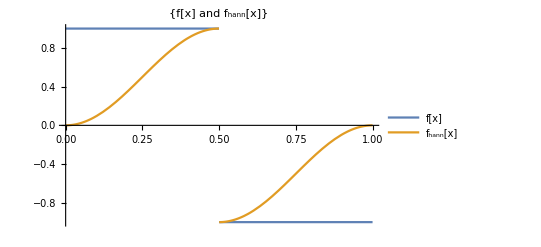

```mathematica
(*part b*)
g[x_]:=1/2 f[x]*(1 - Cos[2*Pi*x])                           (* Defines the hann function *)
Plot[{f[x], g[x]}, {x, 0, 1}, PlotLegends->{"f[x]", "f_hann[x]"}, PlotLabel->{"f[x] and f_hann[x]"}]  
bk[k_,L_] := 2/L*∫_0^L g[x]Cos[(2*k*Pi*x)/L] ⅆx         (* Defines the function Subscript[b, k]*)
 Bk= Range[11];
For [i=0, i ≤ 10, i++, Bk[[i]] = bk[i, 1]]         (* Precomputes Subscript[a, k] for k=1 to 10*)
ck[k_,L_] :=2/L*∫_0^L g[x]Sin[(2*k*Pi*x)/L]ⅆx                    (* Defines the function Subscript[c, k]*)
Ck = Range[11];
For [j=0, j ≤ 10, j++, Ck[[j]] = ck[j, 1]]        (* Precomputes Subscript[c, k] for k=1 to 10*)
Subscript[F, y][n_] :=Bk[[0]]/2+∑_(k=1)^n (Bk[[k]]*Cos[2*k*Pi*x] + Ck[[k]]*Sin[2*k*Pi*x])      (* Computes the Fourier series*)
Subscript[F, hann][n_, z_] := Subscript[F, y][n]/.x->z                                   (* Overlays it with the real axis*)
Manipulate[                                    (* Uses manipulate to plot the function for n=1 to 10*)
Plot[{Subscript[F, hann][n, t], g[t]}, {t, 0, 1}, PlotLegends->{"F_(hann,  n)", "f_hann"},
PlotLabel->"F_(hann,  n) and f_hann"], {n, 1, 10, 1}]
```

Best Fit of e_F[n] in the form A/n+b is:

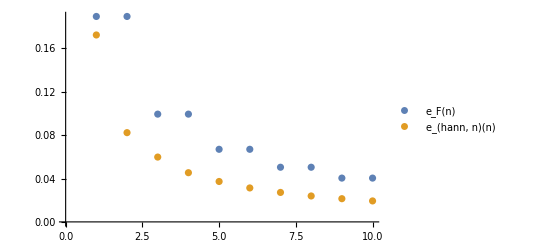

0.0355003+0.183709/x

Best Fit of e_hann[n] in the form A/n+b is:

0.0027995+0.168041/x

The limit as e_F[n] approaches ∞ is:

0.0355003

The limit as e_hann[n] approaches ∞ is:

0.0027995

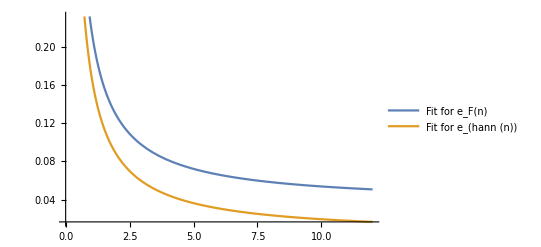

```mathematica
(* part c*)
hh[n_]:=∫_0^1 (Subscript[F, fourier][n, x] - f[x])^2 ⅆx                         (* Define the error function between f[x] and Subscript[f, n][x]*)
Subscript[hh, list]={hh[1], hh[2], hh[3], hh[4], hh[5], hh[6], hh[7], hh[8], hh[9], hh[10]}; (* Compute the errors for n = 1..10 *)
hk[n_]:=∫_0^1 (Subscript[F, hann][n, x] - g[x])^2 ⅆx                               (* Define the error function between Subscript[f, hann][x] and Subscript[f, hann,n][x]*)
Subscript[hk, list]={hk[1], hk[2], hk[3], hk[4], hk[5], hk[6], hk[7], hk[8], hk[9], hk[10]};   (* Compute the errors for n = 1..10 *)
Text["Best Fit of e_F[n] in the form A/n+b is:"]
ListPlot[{Subscript[hh, list], Subscript[hk, list]}, PlotLegends->{"e_F(n)", "e_(hann, n)(n)"}]    (* Plots the scattered points of Subscript[e, F](n) and Subscript[e, hann,n](n) for n=1...10*)
Subscript[hh, fit]=Fit[Subscript[hh, list], {1,1/x}, x]            (* Computes the best-fit line for Subscript[e, F][n] *)
Text["Best Fit of e_hann[n] in the form A/n+b is:"]
Subscript[hk, fit]=Fit[Subscript[hk, list], {1,1/x}, x]            (* Computes the best-fit line for Subscript[e, hann,n][n] *)
Text["The limit as e_F[n] approaches ∞ is:"]
Subscript[hh, limit] = Limit[Subscript[hh, fit],x->∞]            (* Computes the limit for the best-fit line of Subscript[e, F][n] as n -> infinity *)
Text["The limit as e_hann[n] approaches ∞ is:"]
Subscript[hh, limit] = Limit[Subscript[hk, fit],x->∞]              (* Computes the limit for the best-fit line of Subscript[e, hann,n][n] as n -> infinity *)
Plot[{Subscript[hh, fit], Subscript[hk, fit]}, {x, 0, 12}, PlotLegends->{"Fit for e_F(n)", "Fit for e_(hann (n))"}]
```

```mathematica
(*part d*)

q[x_]:=Piecewise[{{x, x<2.5}, {5-x, x≥2.5}}]
Subscript[q, c][k_] := 2/5*∫_0^5 q[x]Sin[(k*Pi*x)/5] ⅆx         (* Defines the function Subscript[a, k]*)
qlist = Range[30];
For [j=0, j ≤ 30, j++, qlist[[j]] = Subscript[q, c][j]]        (* Precomputes Subscript[b, k] for k=1 to 10*)
Subscript[q, fourier][n_] := ∑_(b=1)^n (qlist[[b]]*Sin[(b*Pi*x)/5 ])  (* Computes the Fourier series*)
Subscript[q, fourier][n_, z_] := Subscript[q, fourier][n]/.x->z                                   (* Overlays it with the real axis*)

Manipulate[                                    (* Uses manipulate to plot the function for n=1 to 10*)
Plot[{Subscript[q, fourier][n, t], q[t]}, {t, 0, 5}, PlotLegends->{"F_fourier of the heat function", "heat function"},
PlotLabel->"heat function and fourier heat function"], {n, 1, 30, 1}]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{u→InterpolatingFunction[{{0., 5.}, {0., 10.}}, <>]}}

Sum::div: Sum does not converge.

NSum::nsnum: Summand (or its derivative) ⅇ^(-0.395038 k^2) Sin[0.000224624 k] 0[2.02642,0.,-0.225158,0.,0.0810569,0.,-0.0413556,0.,0.0250176,0.,«20»][k] is not numerical at point i = 1.

NSum::nsnum: Summand (or its derivative) 2.71828^(-0.395038 k^2) Sin[0.000224624 k] 0.[2.02642,0.,-0.225158,0.,0.0810569,0.,-0.0413556,0.,0.0250176,0.,«20»][k] is not numerical at point i = 1..

General::stop: Further output of NSum::nsnum will be suppressed during this calculation.

Sum::div: Sum does not converge.

-Graphics3D-